## Settings

```mathematica
imgsize=700;
```

```mathematica
eqn = D[D[f[x],x],x]-( a k Cot[k x]+i(omegam - a Sin[k x]Cos[2thetam]) a Sin[k x] )D[f[x],x]+(Sin[2 thetam]/2)^2 a^2 Sin[k x]^2 f[x]==0
```

1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0

```mathematica
DSolve[eqn,f[x],x]
```

DSolve[1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0,f[x],x]

```mathematica
DSolve[f[x]+x D[f[x],x]==omegam/2-deltalambda[x]Sin[2thetam]/2,f[x],x]
```

{{f[x]→C[1]/x+(∫_1^x 1/2 (omegam-deltalambda[K[1]] Sin[2 thetam])ⅆK[1])/x}}

```mathematica
sys=I D[{phi1[x],phi2[x]},x]=={{0,(g0R+I g0I) Exp[I(-omegam+n0 k)x]},{(g0R-I g0I) Exp[-I(-omegam+n0 k)x],0}}.{phi1[x],phi2[x]}
```

{ⅈ phi1'[x],ⅈ phi2'[x]}=={ⅇ^(ⅈ (k n0-omegam) x) (ⅈ g0I+g0R) phi2[x],ⅇ^(-ⅈ (k n0-omegam) x) (-ⅈ g0I+g0R) phi1[x]}

```mathematica
DSolve[sys,{phi1,phi2},x]
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

```mathematica
%//FullSimplify
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

## Understand The Hamiltonian

```mathematica
ClearAll[k,x,phi,function1,constant1]
DSolve[I D[function1[x],x]==constant1 Sin[k x+phi]function1[x],function1,x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-ⅈ constant1 (-(Cos[phi] Cos[k x])/k+(Sin[phi] Sin[k x])/k)) C[1]]}}

```mathematica
ClearAll[a,k,x,phi,function1,constant1]
DSolve[D[D[function1[x],x],x]-D[a Sin[k x + phi],x]/(a Sin[k x + phi])D[function1[x],x]==-Sin[2thetam]^2/4(a Sin[k x + phi])^2 function1[x],function1,x]
```

{{function1→Function[{x},C[1] Cos[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]-C[2] Sin[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]]}}

## Constant Matter ‘Perturbation’

```mathematica
ClearAll[k,x,phi,function1,function2,constant1]
DSolve[I D[{function1[x],function2[x]},x]==Sin[2thetam]/2 lambdac{{0,Exp[I Cos[2thetam]lambdac x-I omegam x]},{Exp[-I Cos[2thetam]lambdac x + I omegam x],0}}.{function1[x],function2[x]},{function1,function2},x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1]+ⅇ^(1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2]],function2→Function[{x},1/lambdac ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1] (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]+1/lambdac ⅈ ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]+1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2] (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]]}}

## Investigate Resonance

Define the amplitude

```mathematica
ClearAll[khat,ahat,thetam,thetamV,zk,n0,x,phi,function1,function2,constant1]
```

```mathematica
thetamV=Pi/5;
aV=1;
phiV=0;
```

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/2 ahat Sin[2thetam](2n0)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = ( Abs[fun[khat,ahat,thetam,n0]]^2)/( Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/((-1+khat n0)^2+Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2)

```mathematica
(*Limit[amplitude[k,a,t,Round[k]],k->Infinity]*)
```

```mathematica
Limit[amplitude[k,a,t,Round[k]],t->0]
(*Limit[amplitude[k,a,t],t->Pi/4]*)
```

0

```mathematica
Table[{amplitude[k,0.1,Pi/5,Round[k]],k},{k,0.1,1,0.1}]
```

{{0.,0.1},{0.,0.2},{0.,0.3},{0.,0.4},{0.,0.5},{0.0139269,0.6},{0.0244978,0.7},{0.0534881,0.8},{0.18438,0.9},{1.,1.}}

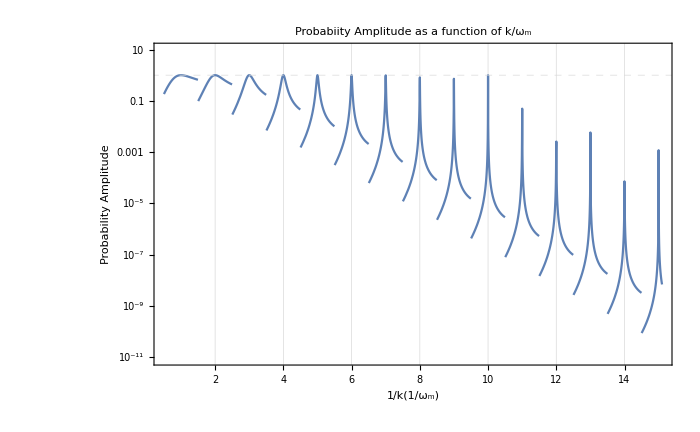

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(1/ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m"]
```

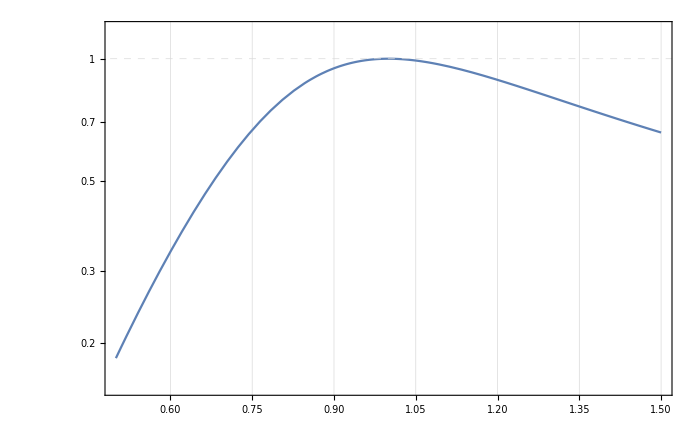

```mathematica
LogPlot[amplitude[1/k,aV,thetamV,Round[k]],{k,0.5,1.5},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]]
```

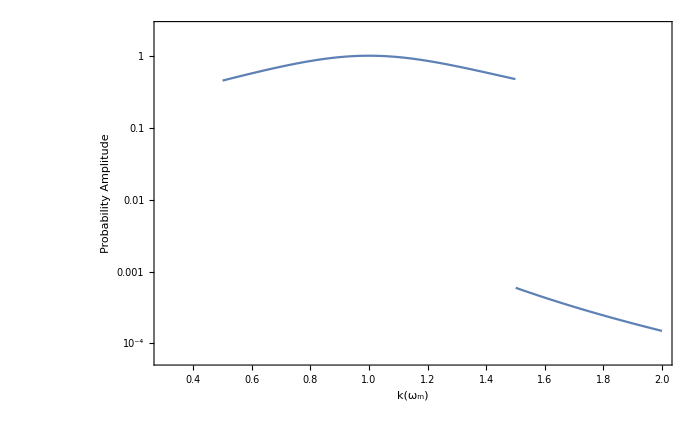

```mathematica
LogPlot[amplitude[k,aV,thetamV,Round[k]],{k,0.3,2},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full]
```

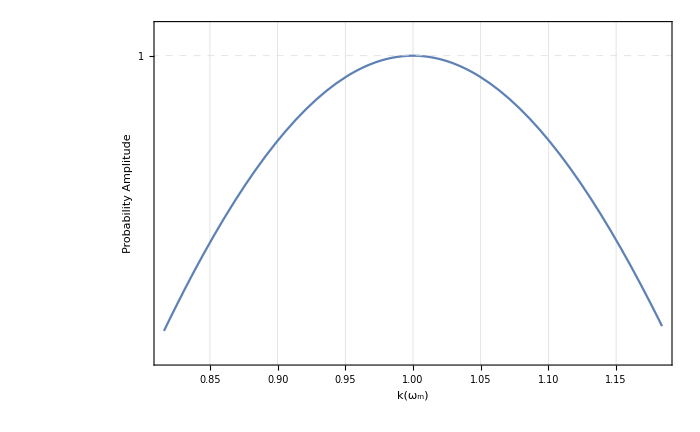
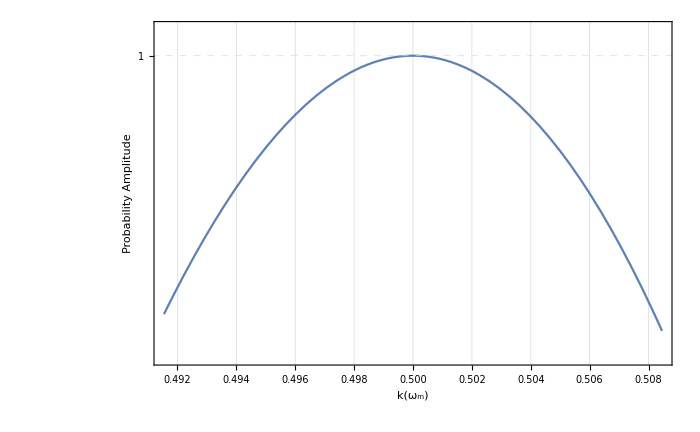
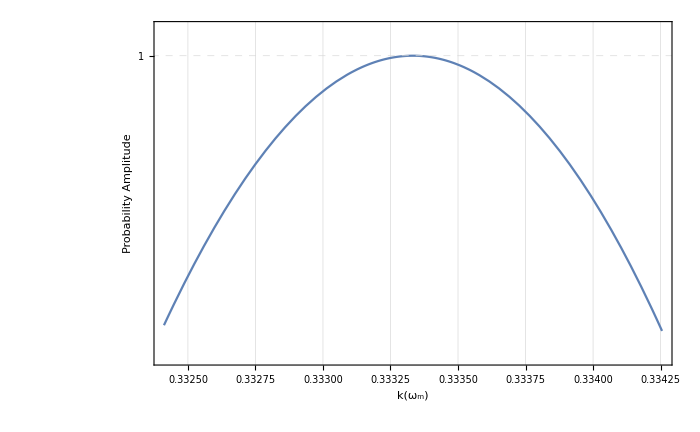
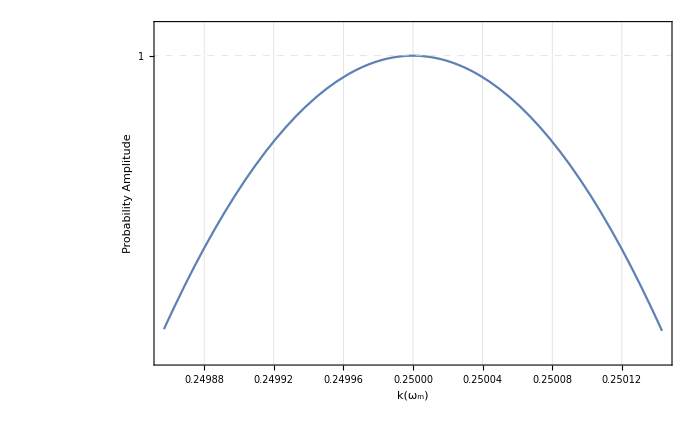

```mathematica
Table[LogPlot[amplitude[k,aV,thetamV,n],{k,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n},FrameLabel->{"k(ω_m)","Probability Amplitude"},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]],{n,1,4}]
```

```mathematica
Series[BesselJ[0,x],{x,0,3}]
```

1-x^2/4+O[x]^4

```mathematica
Limit[BesselJ[0,x]/x,x->0]
```

∞

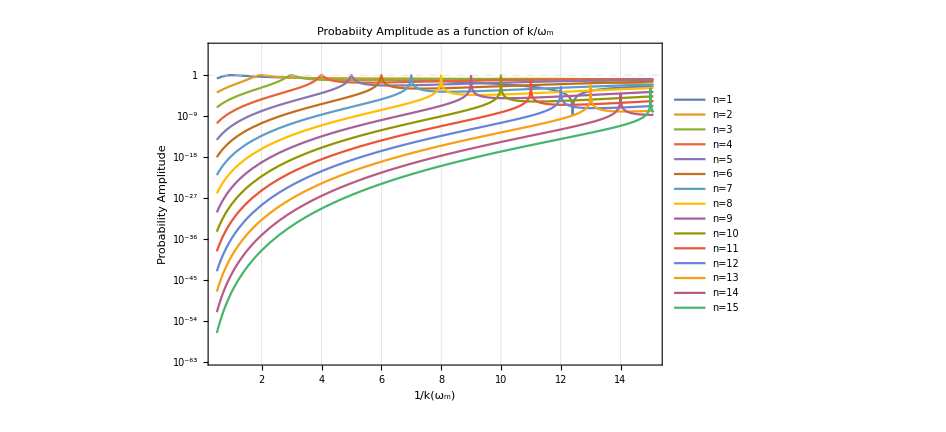

```mathematica
listFunctions=Table[amplitude[1/k,aV,thetamV,n],{n,1,15,1}];
listFunctionsLegends=Table["n="<>ToString@n,{n,1,15,1}];
LogPlot[listFunctions,{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"1/k(ω_m)","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m",PlotLegends->listFunctionsLegends]
```

### Investigation on Width

Looking for the width

```mathematica
aWV=0.1
endpointWList=10
```

0.1

10

```mathematica
fwhm[n_]:=First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-1/n)/n&&k<(1+1/n)/n, k]}]
fwhmRange[n_]:=First@Differences[k/.{ToRules@Reduce[amplitude[k,aWV,thetamV, n] == 0.5&&k>(1-0.5/Exp[n]/n^2)/n&&k<(1+0.5/Exp[n]/n^2)/n, k]}]
fwhmFR[n_]:=2*(k - n) /. FindRoot[amplitude[k,aWV,thetamV, n] == 0.5, {k,1/n,(1-0.5/Exp[n]/n^2)/n,(1+0.5/Exp[n]/n^2)/n}];
```

```mathematica
fwhm[1]
fwhmRange[1]
fwhm[2]
```

0.0950942

0.0950942

0.001469

```mathematica
widthList=Table[{i,fwhmRange[i]},{i,1,endpointWList}] (*For pertubation amplitude equals 0.1*)
(*widthList=Table[{i,fwhm[i]},{i,1,endpointWList}]*) (*For large perturbation amplitude*)
widthListLog=Table[{widthList[[i,1]],Log@widthList[[i,2]]},{i,1,endpointWList}];
widthLine=Fit[widthListLog,{1,x},x];(*Fit data of {x,Log[y]}*)
```

{{1,0.0950942},{2,0.001469},{3,0.0000340384},{4,9.34761×10^-7},{5,2.82022×10^-8},{6,9.03355×10^-10},{7,3.01608×10^-11},{8,1.03811×10^-12},{9,3.6568×10^-14},{10,k/.{ToRules[Reduce[(100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)/((-1+10 k)^2+100 (5+2 √5) Abs[k BesselJ[10,0.0309017/k]]^2)==0.5&&k>0.1&&k<0.1,k]]}}}

$Aborted

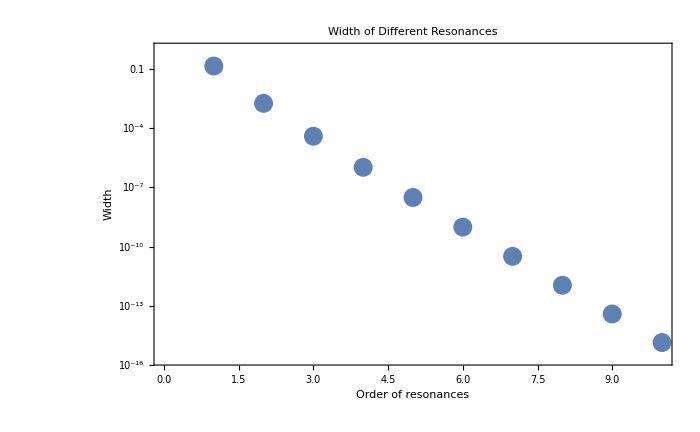

```mathematica
widthListPlt=ListLogPlot[widthList,ImageSize->imgsize,Frame->True,FrameLabel->{"Order of resonances","Width"},PlotLabel->"Width of Different Resonances"]
```

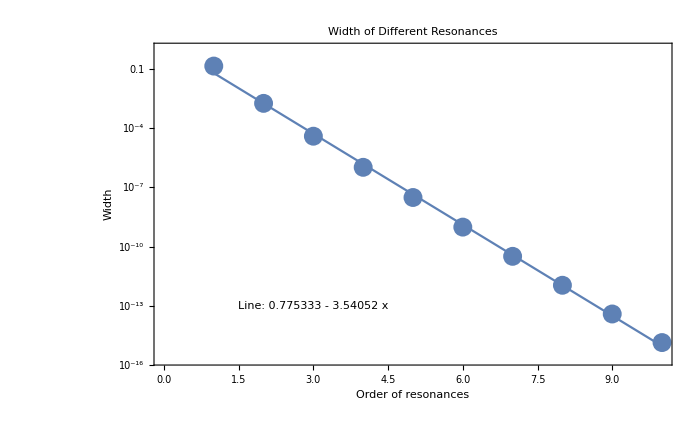

```mathematica
widthLinePlt=Plot[widthLine,{x,1,10},ImageSize->imgsize,Frame->True];
Show[widthListPlt,widthLinePlt,Epilog->Inset[Framed[Style["Line: "<>ToString[widthLine],20],Background->White],{3,-30}]]
```

#### Lorentzian Approximation?

The amplitude has a F^2/(F^2+g^2) form, we assume the bessel function dosn’t change a lot during the resonance. Thus we have the width

```mathematica
widthLor[thetam_,ahat_,n0_]:=N@ahat Sin[2thetam](2n0+1)/(ahat n0 Cos[2thetam])BesselJ[n0,ahat n0 Cos[2thetam]]
```

```mathematica
widthLor[thetamV,aWV,1]
```

0.142641

```mathematica
widthLorList=Table[{i,widthLor[thetamV,aWV,i]},{i,1,10}]
```

{{1,0.142641},{2,0.00367249},{3,0.000119134},{4,4.20642×10^-6},{5,1.55112×10^-7},{6,5.87181×10^-9},{7,2.26206×10^-10},{8,8.82397×10^-12},{9,3.47445×10^-13},{10,1.37804×10^-14}}

```mathematica
widthDiffList=Table[{i,(widthList[[i,2]]-widthLorList[[i,2]])/widthList[[i,2]]},{i,1,10}]
```

{{1,-1.83671×10^-6},{2,-0.999987},{3,-2.},{4,-3.},{5,-4.},{6,-5.},{7,-6.},{8,-6.99992},{9,-8.00254},{10,-9.03011}}

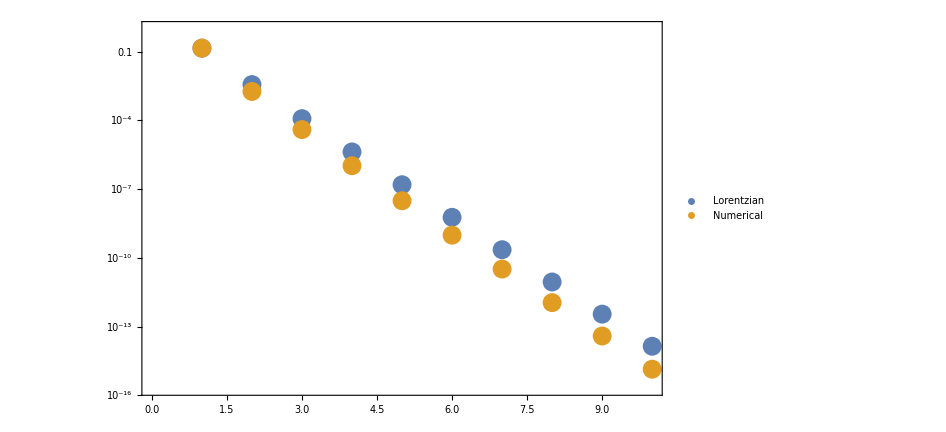

```mathematica
ListLogPlot[{widthLorList,widthList},PlotLegends->{"Lorentzian","Numerical"},Frame->True,ImageSize->imgsize]
ListPlot[widthDiffList,PlotRange->Full];
```

#### What is Bessel Function

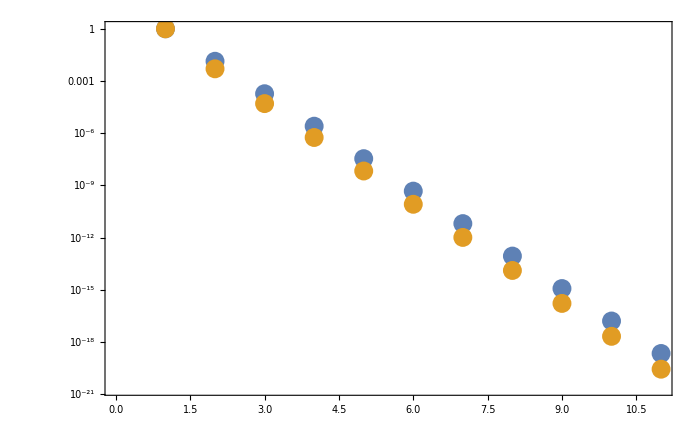

```mathematica
delta=0.01;
besselJApprox[n_]:=Exp[n](delta/2)^n;
ListLogPlot[{Table[besselJApprox[n],{n,0,10}],Table[BesselJ[n,n*delta],{n,0,10}]},Frame->True,ImageSize->imgsize]
```

## Comparing Numerical with Approximation

```mathematica
thetamN=Pi/6;
aN=0.1;
phiN=0;
kN=0.98;
endpointN=100;
init={psi1[0],psi2[0]}=={1,0};
```

```mathematica
amplitude[kN,aN,thetamN,1]
```

0.824081

```mathematica
probApprox[x_,nN_]:=amplitude[kN,aN,thetamN,nN](Sin[Sqrt[ Abs[fun[kN,aN,thetamN,nN]]^2+(nN kN - 1)^2]x/2])^2;
```

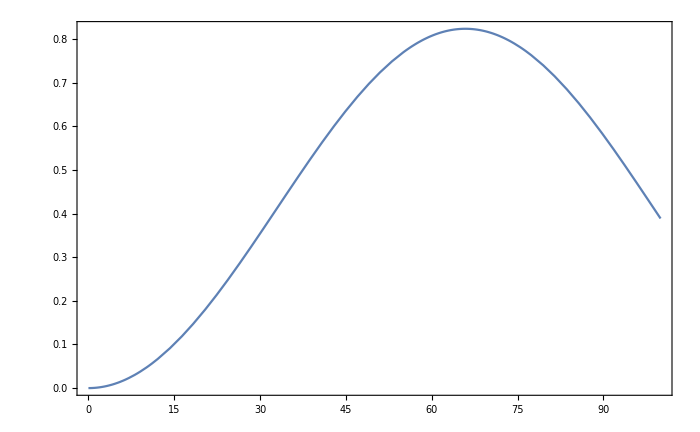

```mathematica
pltProbApprox=Plot[probApprox[x,1],{x,0,endpointN},Frame->True,ImageSize->imgsize]
```

```mathematica
hN[x_]:=(aN Sin[kN x+phiN])Sin[2thetamN]Exp[I(-x-Cos[2thetamN] aN/kN Cos[kN x+phiN])]/2;
```

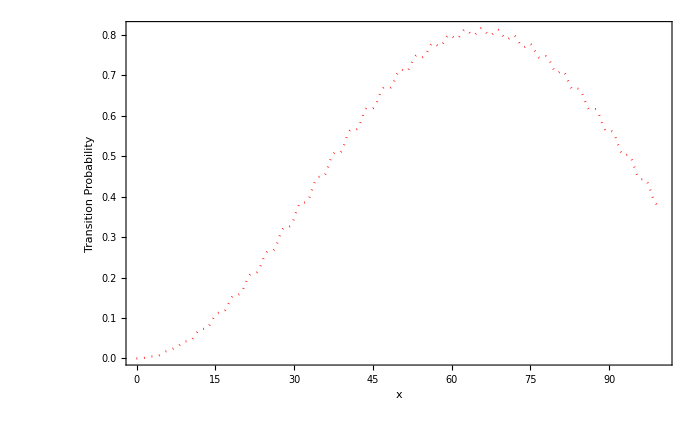

```mathematica
solN=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hN[x]},{Conjugate[hN[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointN}];

pltN=Plot[Evaluate[Abs[psi2[x]]^2/.solN],{x,0,endpointN},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->{Dotted,Red}]
```

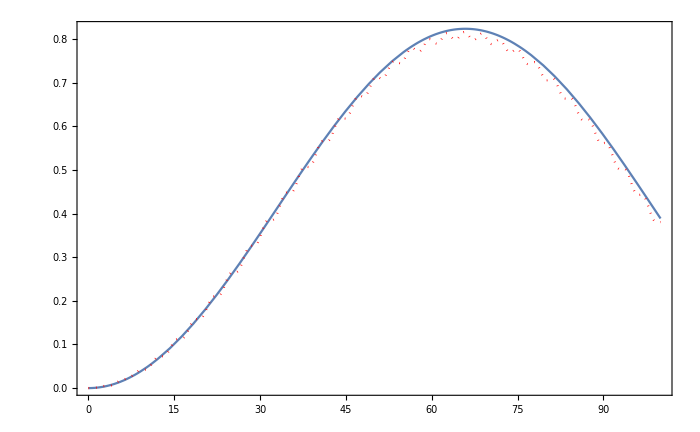

```mathematica
Show[pltProbApprox,pltN]
```